```mathematica
Integrate[Exp[-I*xi*r*Cos[t]],{t,0,2Pi}]
```

ConditionalExpression[2 π BesselJ[0,r xi], r xi∈ℝ]

```mathematica
Integrate[BesselJ[0,r*xi],{xi,0,Infinity}]
```

ConditionalExpression[Piecewise[{{-1/r, Re[r]<0&&Im[r]==0}, {1/r, True}}], r∈ℝ]

```mathematica
Solve[x^5-1==0,x]
```

{{x→1},{x→-(-1)^(1/5)},{x→(-1)^(2/5)},{x→-(-1)^(3/5)},{x→(-1)^(4/5)}}

```mathematica
N[{{x->1},{x->-(-1)^(1/5)},{x->(-1)^(2/5)},{x->-(-1)^(3/5)},{x->(-1)^(4/5)}}]
```

{{x→1.},{x→-0.809017-0.587785 ⅈ},{x→0.309017+0.951057 ⅈ},{x→0.309017-0.951057 ⅈ},{x→-0.809017+0.587785 ⅈ}}

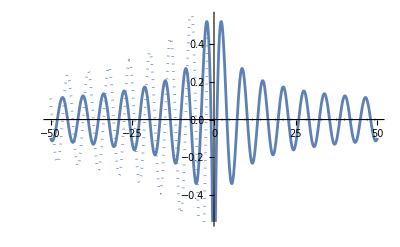

```mathematica
ReImPlot[BesselY[0,x],{x,-50,50}]
```

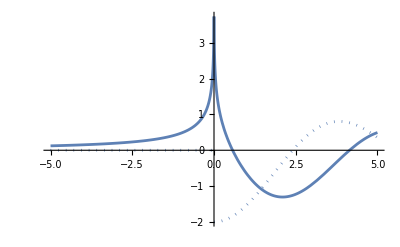

```mathematica
ReImPlot[StruveH[0,-x]-BesselY[0,-x],{x,-5,5}]
```

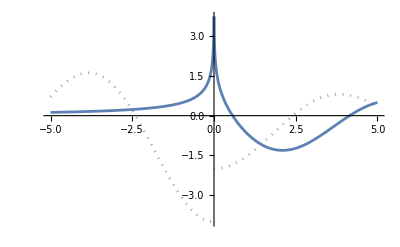

```mathematica
ReImPlot[-StruveH[0,x]-BesselY[0,x]-2I BesselJ[0,x],{x,-5,5}]
```

```mathematica
x = 3 + 2I;
N[StruveH[0,x]-BesselY[0,x]];
N[BesselJ[0,x] + I*StruveH[0,x]]
```

0.0700183+0.19884 ⅈ

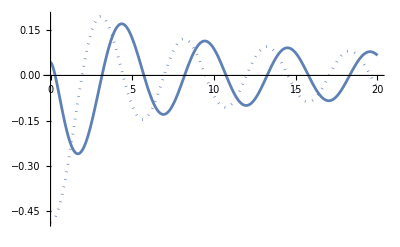

```mathematica
b = 2;
g = -0.5;
p0 =( y^5 -b y+g == 0);
rts = List @@ NRoots[p0,y][[All,2]];
pf = 1./ (5*rts^4-b);
ReImPlot[Sum[Pi/2 pf[[i]]rts[[i]]^2*(StruveH[0,-rts[[i]]*x] - BesselY[0,-rts[[i]]*x]),{i,1,5}] ,{x, 0, 20}]
```

```mathematica
rts
```

{-1.11616,-0.250493,0.0608855-1.19702 ⅈ,0.0608855+1.19702 ⅈ,1.24488}

```mathematica
b = 2;
g = -0.5;
p0 =( y^5 -b y+g == 0);
rts = List @@ NRoots[p0,y][[All,2]];
pf = 1./ (5*rts^4-b);
ReImPlot[Sum[Pi/2 pf[[i]]rts[[i]]^2*(StruveH[0,-rts[[i]]*x] - BesselY[0,-rts[[i]]*x]),{i,1,5}] ,{x, 0, 20}]
```

-Graphics-

```mathematica
rts
```

{-0.910273-0.608707 ⅈ,-0.910273+0.608707 ⅈ,0.304724-1.13327 ⅈ,0.304724+1.13327 ⅈ,1.2111}

```mathematica
N[StruveH[0,-rts[[3]]]-BesselY[0,-rts[[3]]]]
```

0.118432-0.598192 ⅈ

```mathematica
N[StruveH[0,-rts[[5]]]-BesselY[0,-rts[[5]]]]
```

-0.887443-1.33117 ⅈ

```mathematica
rts[[5]]
```

1.2111

```mathematica
x =3 - 2I;
N[StruveH[0,-x]-BesselY[0,-x]]
```

-0.25166-0.0522251 ⅈ

```mathematica
x =3 ;
N[StruveH[0,-x]-BesselY[0,-x]]
```

-0.951156+0.520104 ⅈ

```mathematica
x =-2 ;
N[StruveH[0,x]-BesselY[0,x]]
```

-1.30123-0.447782 ⅈ

```mathematica
x =2 ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.753796

```mathematica
x =-2-2I ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.562762-0.179132 ⅈ

```mathematica
x =-2+I;
N[BesselJ[1,x]+I StruveH[1,x]]
```

-0.261584+0.611786 ⅈ

```mathematica
x =2+I ;
N[StruveH[1,x]-BesselY[1,x]]
```

0.708034-0.0703676 ⅈ

```mathematica
FourierTransform[1/(-rho - rhoj), rho, xi]
```

ⅈ ⅇ^(-ⅈ rhoj xi) √(π/2) (Sign[xi] (-1+Sign[Abs[Im[rhoj]]])+2 HeavisideTheta[-xi Sign[Im[rhoj]]] Sign[Im[rhoj]])

```mathematica
Integrate[BesselJ[0, q]*Exp[-I*xi*q],{q, -Infinity,  Infinity}]
```

ConditionalExpression[2/(√(1-xi^2)), -1<Re[xi]<1&&Im[xi]==0]

```mathematica
Integrate[2*xi/2/(1-xi^2)*Exp[I*xi*x]*(-I*Sign[xi]),{xi,-0.5,0.5}] // Simplify
```

(0.-0.5 ⅈ) ⅇ^((0.-1. ⅈ) x) (-1. ⅇ^((0.+2. ⅈ) x) ExpIntegralEi[(0.-0.5 ⅈ) x]-1. ExpIntegralEi[(0.+0.5 ⅈ) x]+2. ⅇ^((0.+2. ⅈ) x) ExpIntegralEi[(0.-1. ⅈ) x]+2. ExpIntegralEi[(0.+1. ⅈ) x]-1. ⅇ^((0.+2. ⅈ) x) ExpIntegralEi[(0.-1.5 ⅈ) x]-1. ExpIntegralEi[(0.+1.5 ⅈ) x])

```mathematica
Integrate[BesselJ[0,x]*Exp[ -I*xi*x],{x,-Infinity,Infinity}] // Simplify
```

ConditionalExpression[2/(√(1-xi^2)), -1<Re[xi]<1&&Im[xi]==0]

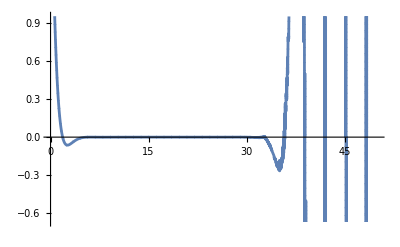

```mathematica
rhoj = 1+I;
ReImPlot[StruveH[0,-rhoj*x]-BesselY[0,-rhoj*x] + I*(StruveH[0,-Conjugate[rhoj]*x]-BesselY[0,-Conjugate[rhoj]*x]),{x,0,50}]
```

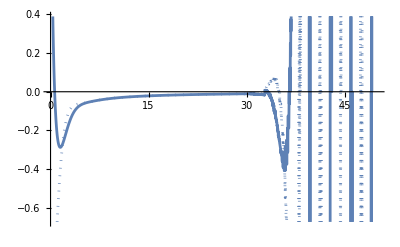

```mathematica
ReImPlot[I*(StruveH[0,-Conjugate[rhoj]*x]-BesselY[0,-Conjugate[rhoj]*x]),{x,0,50}]
```

```mathematica
rhoj = 1;
ReImPlot[StruveK[0,-Conjugate[rhoj]*x],{x,0,60}]
```

-Graphics-

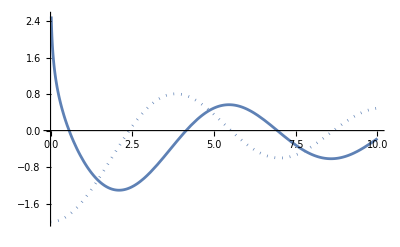

```mathematica
rhoj = 1;
 ReImPlot[(StruveH[0,-rhoj*x]-BesselY[0,-rhoj*x]),{x,0,10}]
```

```mathematica
ConditionalExpression[2/(√(1-xi^2)), -1<Re[xi]<1&&Im[xi]==0]
```

```mathematica
Integrate[2/(√(1-xi^2))Exp[I*xi*x],{xi, -1,1}]
```

2 π BesselJ[0,x]

```mathematica
Integrate[-2/(√(1-xi^2))Exp[I*xi*x]*I*Sign[xi]*Exp[-I*rhoj*xi],{xi, -1,1}]
```

-2 π StruveH[0,1-x]

```mathematica
Integrate[BesselJ[0,r* q]*Exp[-I*xi*q],{q, -Infinity,  Infinity}]
```

ConditionalExpression[2/(√(r^2-xi^2)), xi^2<r^2&&r>0]

```mathematica
Integrate[1/q*Exp[-I*xi*q],{q, -Infinity,  Infinity}, PrincipalValue->True]
```

ConditionalExpression[-Log[ⅈ xi]+Log[Abs[xi]]-1/2 ⅈ π Sign[xi], xi∈ℝ]

```mathematica
Integrate[2/(√(r^2-xi^2))*Exp[I*xi*x],{xi, -r,  r}]
```

ConditionalExpression[2 π BesselJ[0,x Abs[r]], r∈ℝ]

```mathematica
I/ 2 Integrate[2/(√(r^2-xi^2))*Exp[I*xi*x]*Sign[xi],{xi, -r,  r}]
```

ConditionalExpression[ⅈ π StruveL[0,ⅈ x Abs[r]], r∈ℝ]

```mathematica
Integrate[2/(√(r^2-xi^2))*Exp[I*xi*x]*Sign[xi],{xi, -r,  r}]
```

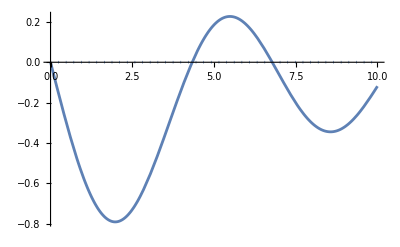

```mathematica
ReImPlot[I*StruveL[0,I*x],{x,0,10}]
```

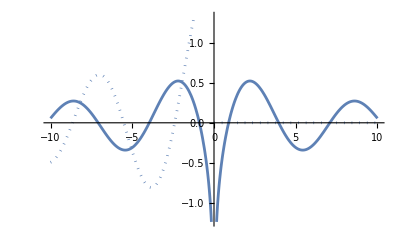

```mathematica
ReImPlot[BesselY[0,x],{x,-10,10}]
```

```mathematica
Integrate[BesselJ[0,rho*r]/(rj - rho),{rho,-Infinity,Infinity}]
```

ConditionalExpression[BesselJ[0,r rj] (-Log[-1/rj]+Log[1/rj])+π StruveH[0,r rj], Im[r]==0&&(Im[rj]≠0||Re[rj]==0)&&Re[r]>0]

```mathematica
N[StruveH[0,2 I]]
```

0.+1.93743 ⅈ

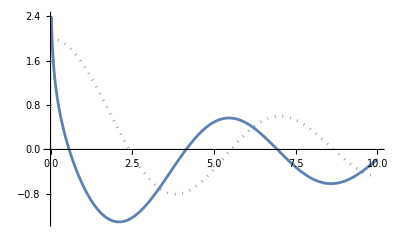

```mathematica
ReImPlot[StruveH[0,-x] - BesselY[0,-x]+4I BesselJ[0,x],{x,0,10}]
```

```mathematica
ReImPlot[-StruveH[0,x] - BesselY[0,x]+2I BesselJ[0,x],{x,0,10}]
```

-Graphics-

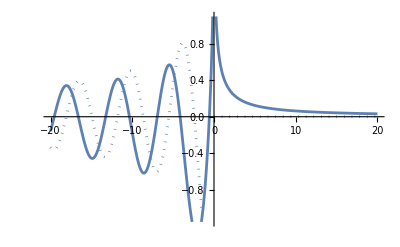

```mathematica
ReImPlot[StruveH[0,x] - BesselY[0,x],{x,-20,20}]
```

```mathematica
Grad[StruveH[0,r(x-y)],{x,y}]
```

{1/2 r (2/π+StruveH[-1,r (x-y)]-StruveH[1,r (x-y)]),-1/2 r (2/π+StruveH[-1,r (x-y)]-StruveH[1,r (x-y)])}

```mathematica
N[StruveH[-1,1]]
```

0.438162

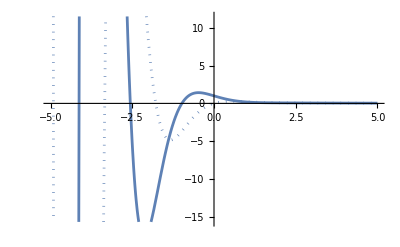

```mathematica
ReImPlot[BesselJ[0,(2+2I)*x] +I* StruveH[0,(2+2I)*x] ,{x,-5,5}]
```

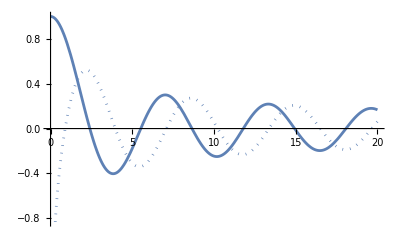

```mathematica
ReImPlot[HankelH1[0,x],{x,0,20}]
```

```mathematica
Integrate[BesselJ[0,x]/(r-x),{x, 0, Infinity}]
```

ConditionalExpression[1/2 (π BesselY[0,r]-2 BesselJ[0,r] (Log[-1/r]+Log[r])+π StruveH[0,r]), Im[r]≠0||Re[r]≤0]

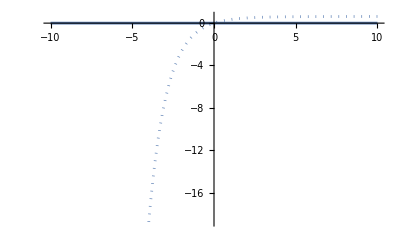

```mathematica
ReImPlot[BesselJ[1,I*x] + I*StruveH[1,I*x],{x,-10,10}]
```

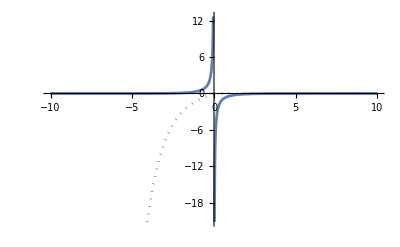

```mathematica
ReImPlot[HankelH1[1,I x],{x,-10,10}]
```

```mathematica
x = 1-I;
N[StruveH[1,x]-BesselY[1,x] ]
```

0.71418+0.208619 ⅈ

```mathematica
rhoj = 2+0.01*I;
r = 0.5;
NIntegrate[BesselJ[0,rho*r]/(rho-rhoj),{rho,0,Infinity}]
- Pi/2(StruveH[0,rhoj*0.5]+BesselY[0,rhoj*r] - 2*I*BesselJ[0,rhoj*r])
```

-1.02499+2.39438 ⅈ

-1.02499+2.39438 ⅈ

0.652529-1.52431 ⅈ

```mathematica
Norm[{2+I,-1,1-I}]
```

2 √2

```mathematica
Norm[{3-2I,I,I}]
```

√15

```mathematica
Conjugate[{2+I,-1,1-I}].{3-2I,I,I}
```

3-7 ⅈ

```mathematica
c = 2;
x2 = 3;
D[StruveH[0,c*Sqrt[x1^2+x2^2]],x1]
```

(x1 (2/π+StruveH[-1,2 √(9+x1^2)]-StruveH[1,2 √(9+x1^2)]))/(√(9+x1^2))

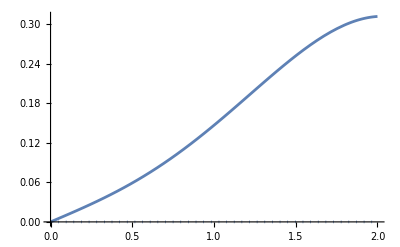

```mathematica
ReImPlot[(x1 (2/π+StruveH[-1,2 √(9+x1^2)]-StruveH[1,2 √(9+x1^2)]))/(√(9+x1^2)),{x1,0,2}]
```

```mathematica
ReImPlot[c*x1/Sqrt[x1^2+x2^2]*(2/Pi - StruveH[1,c*Sqrt[x1^2+x2^2]]),{x1,0,2}]
```

-Graphics-

```mathematica
c = 2;
x2 = 3;
nu = 4;
D[StruveH[nu,c*Sqrt[x1^2+x2^2]],x1]
```

(x1 ((32 (9+x1^2)^2)/(945 π)+StruveH[3,2 √(9+x1^2)]-StruveH[5,2 √(9+x1^2)]))/(√(9+x1^2))

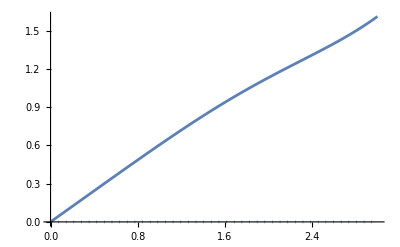

```mathematica
ReImPlot[(x1 ((32 (9+x1^2)^2)/(945 π)+StruveH[3,2 √(9+x1^2)]-StruveH[5,2 √(9+x1^2)]))/(√(9+x1^2)),{x1,0,3}]
```

```mathematica
nu = 4;
ReImPlot[c*x1/Sqrt[x1^2+x2^2]*(StruveH[nu-1,c*Sqrt[x1^2+x2^2]]-nu/(c*Sqrt[x1^2+x2^2])*StruveH[nu,c*Sqrt[x1^2+x2^2]]),{x1,0,3}]
```

-Graphics-

```mathematica
yy=0;
D[StruveH[0,c*Sqrt[xx^2+yy^2]],{xx,2}]
```

-(xx^2 (2/π+StruveH[-1,2 √(xx^2)]-StruveH[1,2 √(xx^2)]))/((xx^2)^(3/2))+(2/π+StruveH[-1,2 √(xx^2)]-StruveH[1,2 √(xx^2)])/(√(xx^2))+(xx ((xx (1/(π √(xx^2))+StruveH[-2,2 √(xx^2)]-StruveH[0,2 √(xx^2)]))/(√(xx^2))-(xx ((4 √(xx^2))/(3 π)+StruveH[0,2 √(xx^2)]-StruveH[2,2 √(xx^2)]))/(√(xx^2))))/(√(xx^2))

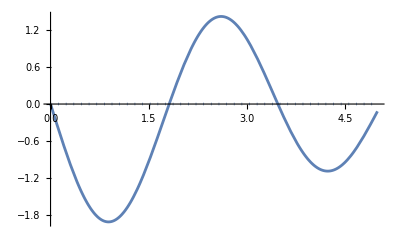

```mathematica
ReImPlot[-(xx^2 (2/π+StruveH[-1,2 √(xx^2)]-StruveH[1,2 √(xx^2)]))/((xx^2)^(3/2))+(2/π+StruveH[-1,2 √(xx^2)]-StruveH[1,2 √(xx^2)])/(√(xx^2))+(xx ((xx (1/(π √(xx^2))+StruveH[-2,2 √(xx^2)]-StruveH[0,2 √(xx^2)]))/(√(xx^2))-(xx ((4 √(xx^2))/(3 π)+StruveH[0,2 √(xx^2)]-StruveH[2,2 √(xx^2)]))/(√(xx^2))))/(√(xx^2)),{xx,0,5}]
```

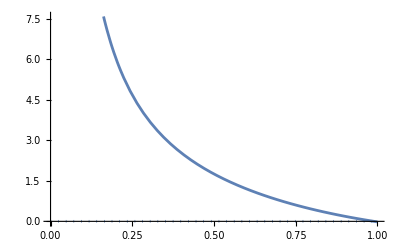

```mathematica
ReImPlot[2c xx^2/Pi/Sqrt[xx^2+yy^2]^3-c^2yy^2/(xx^2+yy^2)*StruveH[0,c*Sqrt[xx^2+yy^2]]-c(xx^2-yy^2)/Sqrt[(xx^2+yy^2)]^3*StruveH[1,c*Sqrt[xx^2+yy^2]],{xx,0,1}]
```

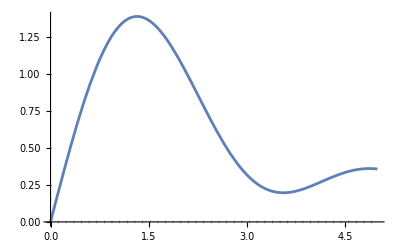

```mathematica
ReImPlot[c(xx^2-yy^2)/Sqrt[(xx^2+yy^2)]^3*StruveH[1,c*Sqrt[xx^2+yy^2]],{xx,0,5}]
```

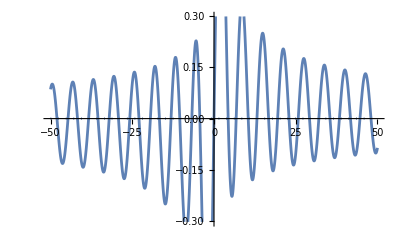

```mathematica
ReImPlot[StruveH[0,x],{x,-50,50}]
```

```mathematica
Plot3D[Im[BesselJ[0, Sqrt[x^2+y^2]] + I*StruveH[0,Sqrt[x^2+y^2]]] ,{x,-4,4},{y,-4,4}]
```

-Graphics3D-

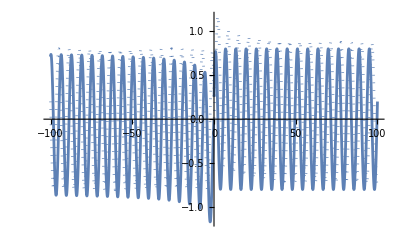

```mathematica
StruveR[nu_,c_,x_,y_] = BesselJ[nu,c* Sqrt[x^2+y^2]] + I*StruveH[nu,c*Sqrt[x^2+y^2]];
DxStruveR[x_,y_] = D[StruveR[x,y], x];
DxxStruveR[x_,y_] = D[StruveR[x,y], {x,2}];
DyyStruveR[x_,y_] =  D[StruveR[x,y], {y,2}];
ReImPlot[Sqrt[x]*StruveR[0,1,x,0],{x,-100,100}]
```

```mathematica
Plot3D[Re[StruveR[1,1,x,y]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[Re[DyyStruveR[x,y]+DxxStruveR[x,y]],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[Re[2I /(Pi*Sqrt[x^2+y^2])-StruveR[x,y]],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

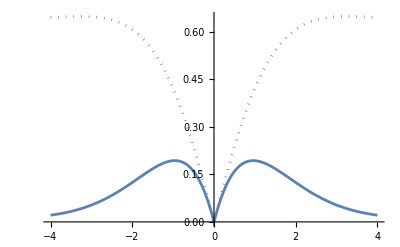

```mathematica
ReImPlot[StruveR[1,1+I,0, x],{x,-4,4}]
```

```mathematica
,
```

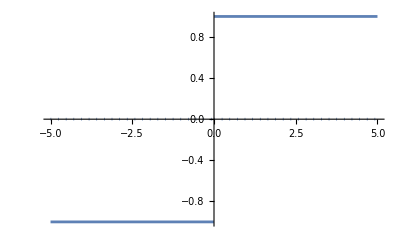

```mathematica
ReImPlot[x/Sqrt[x^2],{x,-5,5}]
```

```mathematica
ReImPlot[Hankel[0,-1-I,0, x],{x,-4,4}]
```

-Graphics-

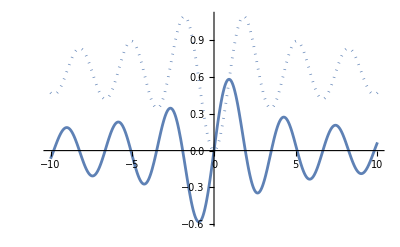

```mathematica
ReImPlot[BesselJ[1,2* x] + I*StruveH[1,2*x],{x,-10,10}]
```

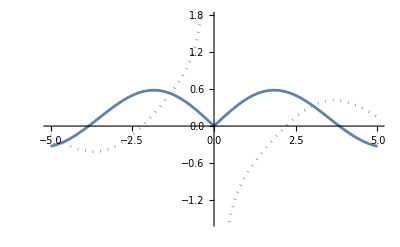

```mathematica
ReImPlot[HankelH1[1,x],{x,-5,5}]
```

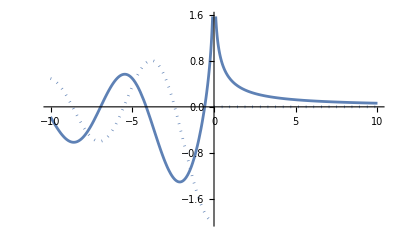

```mathematica
StruveK[n_,r_] =StruveH[n,r] - BesselY[n,r];
ReImPlot[StruveK[0,x],{x,-10,10}]
```

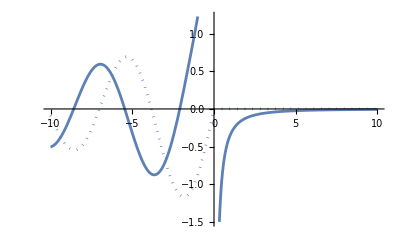

```mathematica
StruveKx[n_,r_] = D[StruveK[n,r],r];
ReImPlot[StruveKx[0,x],{x,-10,10}]
```

```mathematica
ReImPlot[2/Pi-StruveK[1,x],{x,-10,10}]
```

-Graphics-

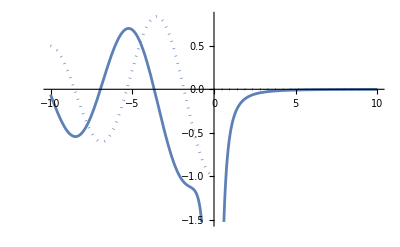

```mathematica
ReImPlot[StruveKx[1,x],{x,-10,10}]
```

```mathematica
ReImPlot[StruveK[0,x] - 1/x StruveK[1,x],{x,-10,10}]
```

-Graphics-

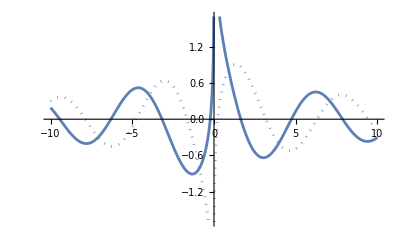

```mathematica
ReImPlot[(1+I)HankelH1[0,x],{x,-10,10}]
```

```mathematica
NIntegrate[100/Sqrt[x^2+y^2]*(x-1/10)^4*(y+1/2)^2*Exp[-40*((x)^2+(y)^2)^4],{x,-1,1},{y,-1,1},MaxRecursion->100,WorkingPrecision->100,AccuracyGoal->16]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 200 recursive bisections in x near {x,y} = {1.050598812843583670671506447090532966185734741075927763182935641002666852555220419140484449193953013×10^-60,0.6882472016116852977216287342936235251268953566156492005616332849725616834004986451036040772397807148}. NIntegrate obtained 1.872542774713242847495187869178061993540400524365678467953930623967837353085031919180297652933705686 and 0.289359714081214126741457782844188517092332458704228779795350655014734867999129018830183689710693594 for the integral and error estimates.

1.872542774713242847495187869178061993540400524365678467953930623967837353085031919180297652933705686

```mathematica
NIntegrate[1/Sqrt[x^2+y^2]Exp[-50*(x^2+y^2)^4-100*x^2],{x,-1,1},{y,-1,1},MaxRecursion->100,WorkingPrecision->100,AccuracyGoal->16]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.2095804366864299557483969220356418170964566677095449913220342123643665139963771408269596871769832445918468204666695053769721464587343662626130793684 and 2.20000486973310287625263553277503468588359379262227800357335923944666866449632914519525064772560618586825783246077511317760155380342481372965161892083×10^-13 for the integral and error estimates.

1.209580436686429955748396922035641817096456667709544991322034212364366513996377140826959687176983245

```mathematica
NIntegrate[Log[Sqrt[x^2+y^2]] Exp[-(x^2+y^2)/(2*5^2)],{x,-40,40},{y,-40,40},WorkingPrecision->40,AccuracyGoal->20]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 261.915156053391649466662397016542869783807274589193948395710125490252609612448944781478319 and 1.70036569024299120321737298951084161739708097991489673709457494956347904938522849368705707×10^-11 for the integral and error estimates.

261.9151560533916494666623970165428697838

```mathematica
Binomial[0.5,1]
```

0.5

```mathematica
Binomial[1.5,2]
```

0.375

```mathematica
Plot3D[Sqrt[(x^2+y^2)]x*y/(x^2+y^2),{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
a = 0.809;
b=-0.221;
NIntegrate[1/Sqrt[x^2+y^2]*(a*Cos[a+x]+b*Sin[b+y])*Exp[-640*((x)^2+(y)^2)^4],{x,-1,1},{y,-1,1},MaxRecursion->100,WorkingPrecision->100,AccuracyGoal->16]
```

```mathematica
val[X_,Y_] = Exp[-(X^2+Y^2)/(2*width^2)];
D[val[x,y],{y,2}]
```

-(ⅇ^((-x^2-y^2)/(2 width^2)))/width^2+(ⅇ^((-x^2-y^2)/(2 width^2)) y^2)/width^4

0

```mathematica
rhow = 1000;
rhoi = 917;
g = 9.8;
w = 1;
Ec = 7*10^9;
nu = 0.3;
H = 20;
alpha = Ec*H^3/(12*(1-nu^2))
beta = rhoi*H*w^2 - rhow*g
gamma = rhow*g
```

5.12821×10^12

8540.

9800.

```mathematica
Ec/(12*(1-nu^2))
```

6.41026×10^8

```mathematica
v1 = {};
```

```mathematica
-1/3*Log[1/3] - 2/3*Log[2/3]
```

2/3 Log[3/2]+Log[3]/3

```mathematica
N[2/3 Log[3/2]+Log[3]/3]
```

0.636514

```mathematica
Log[2]
```

Log[2]

```mathematica
N[Log[2]]
```

0.693147

```mathematica
-1/2 Log[1/2] - 1/2 Log[1/2]
```

Log[2]

```mathematica
N[Log[2]]
```

0.693147

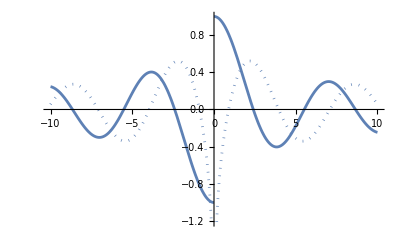

```mathematica
ReImPlot[HankelH1[0,x],{x,-10,10}]
```

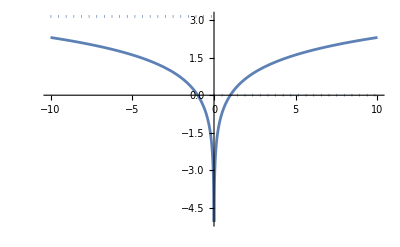

```mathematica
ReImPlot[Log[x],{x,-10,10}]
```

```mathematica
Plot3D[x^2/(x^2+y^2),{x,-5,5},{y,-5,5}]
```

-Graphics3D-